# Project report

## Test chromatogram: temperature control.

D Malan

Department of Chemistry
University of Pretoria

20 February 2020

## Introduction

The quality of the previous chromatogram was hampered by a poorly-defined temperature set point, which caused variable retention times between consecutive GC runs.

## Experimental

### Sample

10% Aromatics in diesel Total™ 50 ppm.

### Temperature program

The chromatography was done with a rather fast temperature ramp. The gradients of the three lines in the figure below are 8200, 5500 and 2100 °C/min.

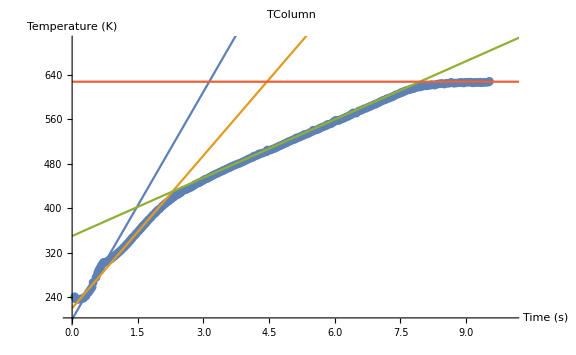

It should be noted that this is the actual temperature, and not the temperature program: the power of the coaxial heater was not enough to control the temperature below 400 K.

### Termination

The SFC×GC run was terminated early by a power cut.

## Results

```mathematica
"C:\\SFC-GC\\Data\\2020_02_19-140031.dat"
```

```mathematica
Show[plot3d, PlotRange->{{750,850},All,All}, ImageSize-> Full]
```

## Discussion

The dead time was set to 11 minutes. This can be increased to 12 minutes.

The improvements in the software to speed up the control loop has brought complications. In some cases the data IDs were lost, because the control loop iterated faster than the data loop. While the chromatogram quality is not affected by this problem, it greatly complicated the production of the chromatogram.

The high temperature ramp was an attempt to improve the sharpness of the early-eluting peaks in the GC chromatograms. This was a partial success. The early peaks are indeed sharper and less “humpy”, but at the cost of narrower peaks overall. This brings the GC peak width close to the time resolution of the software. Data point intervals vary between 20 ms and 50 ms, which means that sometimes there will be fewer than 3 data points per peak. In the 2D chromatogram

The improvement in the set point control is a success. There are no peaks in the chromatogram that were split because of incorrect set point calculations.

## Conclusion

The set point control is now adequate, but there are problems with data integrity.

## Recommendations

Increase the dead time to 12 minutes.

Use a less aggressive temperature ramp.

Slow down the execution of the control loop.

Chain the control loop to the data loop.

Use a buffer to pass instrument states from the control loop to the data loop.

Redesign the cooling system to ensure rapid shut-off of cooling.

Improve coaxial heater power output to ensure controlled temperature under all conditions.